```mathematica
eq=y''[τ]+3 y'[τ] Sqrt[y'[τ]^2+(1/2) (1+Exp[-2 y[τ]])^-2]+Exp[-2 y[τ]] (1+Exp[-2 y[τ]])^-3==0;
```

```mathematica
ics={y[0]==4.0,y'[0]==0.25};
ntau = 4005;
sol=NDSolve[{eq,ics},y,{τ,0,ntau},Method->{"StiffnessSwitching"}];
```

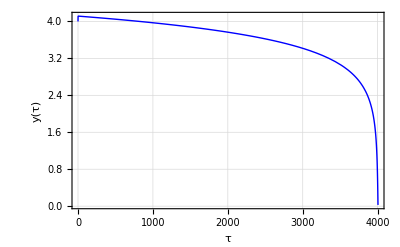

```mathematica
Plot[Evaluate[y[τ]/. sol],{τ,0,ntau},PlotStyle->{Thick,Blue},Frame->True,FrameLabel->{"τ","y(τ)"},LabelStyle->{FontSize->14},GridLines->Automatic,PlotRange->All]
```